## Potential:

```mathematica
Integrate[-2*π*r^2*V0*Exp[-r]*Exp[I*k*r*x],{x,-1,1}];
Integrate[(4 π r V0 Sin[k r] (-Cosh[r]+Sinh[r]))/k,{r,0,∞}];
ConditionalExpression[-(8 π V0)/((1+k^2)^2), -1<Im[k]≤1];
Integrate[-1/2(8 π*M* V0)/((M^2+p^2+q^2-2 p q x)^2),{x,-1,1}];
ConditionalExpression[-(8 M π V0)/((M^2+(p-q)^2) (M^2+(p+q)^2)), ];
V[p_,q0_]:= (-8*π*V0)/((1+p^2+q0^2 - 2*p*q0 + I*eps)*(1+p^2+q0^2 + 2*p*q0 + I*eps));
```

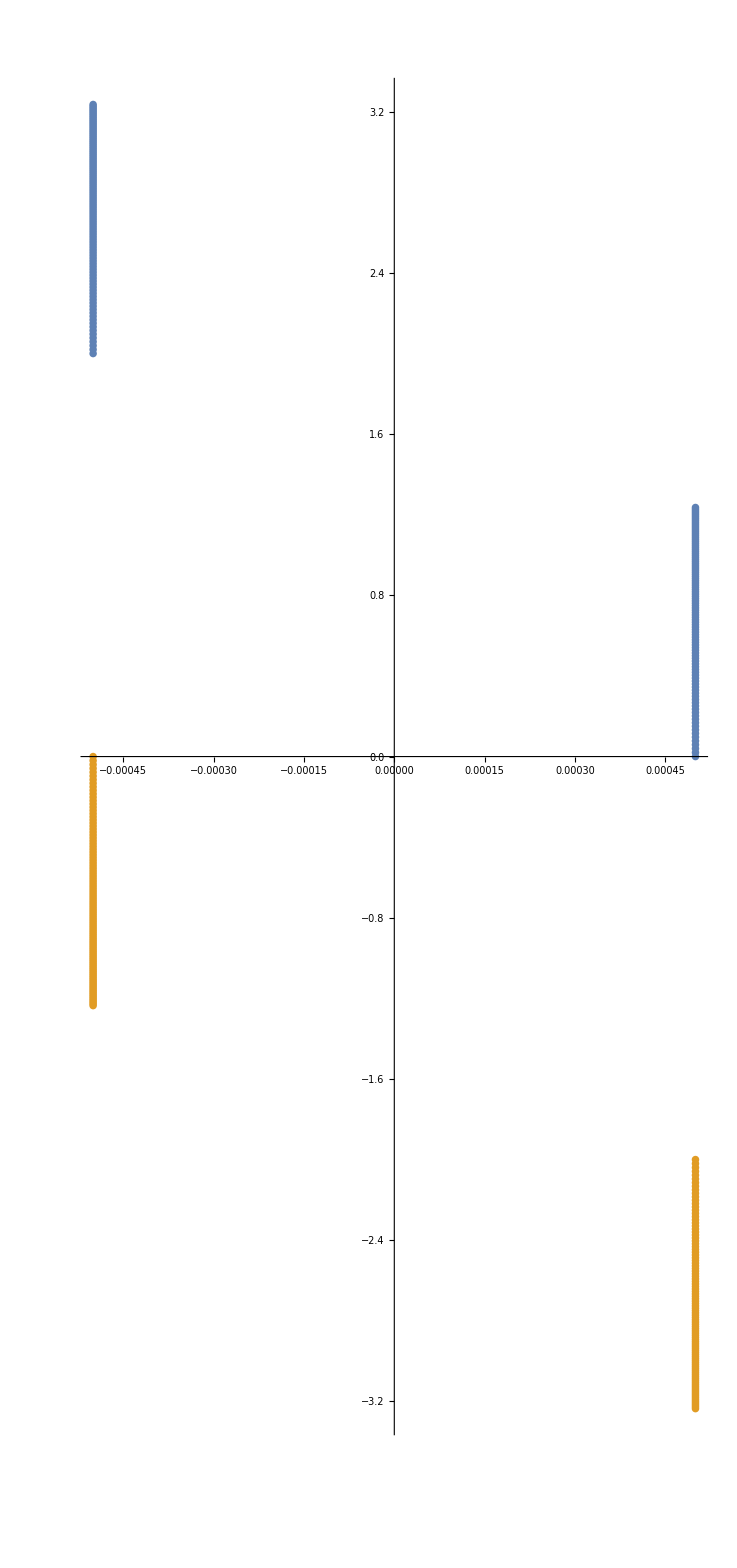

```mathematica
eps = 10^-3;
sol1[q0_]:=Solve[(1+p^2+q0^2 - 2*p*q0 +I*eps)==0 ,p]//N;
sol2[q0_]:=Solve[(1+p^2+q0^2 + 2*p*q0+I*eps)==0 ,p]//N;
q = Array[Sqrt[#]&,100,{-1,-5}]//N;
solution1 = p/.Table[sol1[q0],{q0,q}]//Flatten;
solution2 = p/.Table[sol2[q0],{q0,q}]//Flatten;
ComplexListPlot[{solution1,solution2}]
```

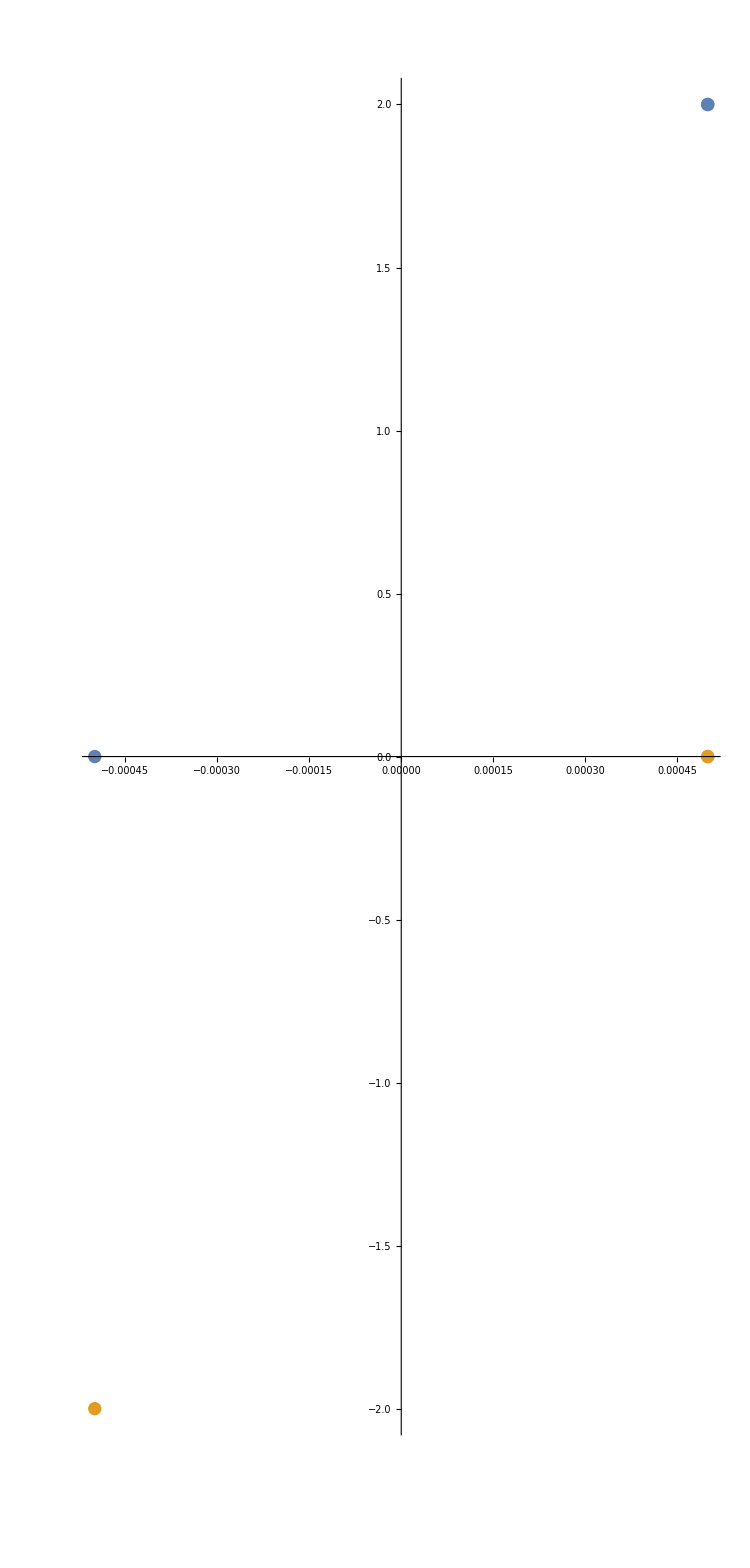

{0.,0.+0.158511 ⅈ,0.+0.224168 ⅈ,0.+0.274549 ⅈ,0.+0.317021 ⅈ,0.+0.354441 ⅈ,0.+0.38827 ⅈ,0.+0.41938 ⅈ,0.+0.448336 ⅈ,0.+0.475532 ⅈ,0.+0.501255 ⅈ,0.+0.52572 ⅈ,0.+0.549097 ⅈ,0.+0.571518 ⅈ,0.+0.593093 ⅈ,0.+0.613909 ⅈ,0.+0.634043 ⅈ,0.+0.653556 ⅈ,0.+0.672504 ⅈ,0.+0.690932 ⅈ,0.+0.708881 ⅈ,0.+0.726387 ⅈ,0.+0.743481 ⅈ,0.+0.76019 ⅈ,0.+0.77654 ⅈ,0.+0.792553 ⅈ,0.+0.808249 ⅈ,0.+0.823646 ⅈ,0.+0.83876 ⅈ,0.+0.853606 ⅈ,0.+0.868199 ⅈ,0.+0.88255 ⅈ,0.+0.896672 ⅈ,0.+0.910574 ⅈ,0.+0.924268 ⅈ,0.+0.937762 ⅈ,0.+0.951064 ⅈ,0.+0.964183 ⅈ,0.+0.977125 ⅈ,0.+0.989899 ⅈ,0.+1.00251 ⅈ,0.+1.01496 ⅈ,0.+1.02727 ⅈ,0.+1.03942 ⅈ,0.+1.05144 ⅈ,0.+1.06332 ⅈ,0.+1.07507 ⅈ,0.+1.08669 ⅈ,0.+1.09819 ⅈ,0.+1.10957 ⅈ,0.+1.12084 ⅈ,0.+1.13199 ⅈ,0.+1.14304 ⅈ,0.+1.15397 ⅈ,0.+1.16481 ⅈ,0.+1.17555 ⅈ,0.+1.18619 ⅈ,0.+1.19673 ⅈ,0.+1.20718 ⅈ,0.+1.21754 ⅈ,0.+1.22782 ⅈ,0.+1.23801 ⅈ,0.+1.24811 ⅈ,0.+1.25814 ⅈ,0.+1.26809 ⅈ,0.+1.27795 ⅈ,0.+1.28775 ⅈ,0.+1.29747 ⅈ,0.+1.30711 ⅈ,0.+1.31669 ⅈ,0.+1.3262 ⅈ,0.+1.33563 ⅈ,0.+1.34501 ⅈ,0.+1.35432 ⅈ,0.+1.36356 ⅈ,0.+1.37274 ⅈ,0.+1.38186 ⅈ,0.+1.39093 ⅈ,0.+1.39993 ⅈ,0.+1.40887 ⅈ,0.+1.41776 ⅈ,0.+1.4266 ⅈ,0.+1.43538 ⅈ,0.+1.4441 ⅈ,0.+1.45277 ⅈ,0.+1.4614 ⅈ,0.+1.46997 ⅈ,0.+1.47849 ⅈ,0.+1.48696 ⅈ,0.+1.49539 ⅈ,0.+1.50376 ⅈ,0.+1.5121 ⅈ,0.+1.52038 ⅈ,0.+1.52862 ⅈ,0.+1.53682 ⅈ,0.+1.54497 ⅈ,0.+1.55308 ⅈ,0.+1.56115 ⅈ,0.+1.56918 ⅈ,0.+1.57716 ⅈ,0.+1.58511 ⅈ,0.+1.59301 ⅈ,0.+1.60088 ⅈ,0.+1.60871 ⅈ,0.+1.6165 ⅈ,0.+1.62425 ⅈ,0.+1.63197 ⅈ,0.+1.63965 ⅈ,0.+1.64729 ⅈ,0.+1.6549 ⅈ,0.+1.66247 ⅈ,0.+1.67001 ⅈ,0.+1.67752 ⅈ,0.+1.68499 ⅈ,0.+1.69243 ⅈ,0.+1.69984 ⅈ,0.+1.70721 ⅈ,0.+1.71455 ⅈ,0.+1.72187 ⅈ,0.+1.72915 ⅈ,0.+1.7364 ⅈ,0.+1.74362 ⅈ,0.+1.75081 ⅈ,0.+1.75797 ⅈ,0.+1.7651 ⅈ,0.+1.7722 ⅈ,0.+1.77928 ⅈ,0.+1.78632 ⅈ,0.+1.79334 ⅈ,0.+1.80033 ⅈ,0.+1.8073 ⅈ,0.+1.81424 ⅈ,0.+1.82115 ⅈ,0.+1.82803 ⅈ,0.+1.83489 ⅈ,0.+1.84173 ⅈ,0.+1.84854 ⅈ,0.+1.85532 ⅈ,0.+1.86208 ⅈ,0.+1.86881 ⅈ,0.+1.87552 ⅈ,0.+1.88221 ⅈ,0.+1.88887 ⅈ,0.+1.89551 ⅈ,0.+1.90213 ⅈ,0.+1.90872 ⅈ,0.+1.91529 ⅈ,0.+1.92184 ⅈ,0.+1.92837 ⅈ,0.+1.93487 ⅈ,0.+1.94135 ⅈ,0.+1.94781 ⅈ,0.+1.95425 ⅈ,0.+1.96067 ⅈ,0.+1.96707 ⅈ,0.+1.97344 ⅈ,0.+1.9798 ⅈ,0.+1.98613 ⅈ,0.+1.99245 ⅈ,0.+1.99874 ⅈ,0.+2.00502 ⅈ,0.+2.01127 ⅈ,0.+2.01751 ⅈ,0.+2.02373 ⅈ,0.+2.02993 ⅈ,0.+2.03611 ⅈ,0.+2.04227 ⅈ,0.+2.04841 ⅈ,0.+2.05453 ⅈ,0.+2.06064 ⅈ,0.+2.06673 ⅈ,0.+2.0728 ⅈ,0.+2.07885 ⅈ,0.+2.08488 ⅈ,0.+2.0909 ⅈ,0.+2.0969 ⅈ,0.+2.10288 ⅈ,0.+2.10885 ⅈ,0.+2.1148 ⅈ,0.+2.12073 ⅈ,0.+2.12664 ⅈ,0.+2.13254 ⅈ,0.+2.13843 ⅈ,0.+2.14429 ⅈ,0.+2.15014 ⅈ,0.+2.15598 ⅈ,0.+2.1618 ⅈ,0.+2.1676 ⅈ,0.+2.17339 ⅈ,0.+2.17916 ⅈ,0.+2.18492 ⅈ,0.+2.19066 ⅈ,0.+2.19639 ⅈ,0.+2.2021 ⅈ,0.+2.2078 ⅈ,0.+2.21348 ⅈ,0.+2.21915 ⅈ,0.+2.2248 ⅈ,0.+2.23044 ⅈ,0.+2.23607 ⅈ}

```mathematica
eps = 10^-3;
sol1[q0_]:=Solve[(1+p^2+q0^2 - 2*p*q0 - I*eps)==0 ,p]//N;
sol2[q0_]:=Solve[(1+p^2+q0^2 + 2*p*q0 - I*eps)==0 ,p]//N;
q = Array[Sqrt[#]&,1,{-1}]//N;
solution1 = p/.Table[sol1[q0],{q0,q}]//Flatten;
solution2 = p/.Table[sol2[q0],{q0,q}]//Flatten;
ComplexListPlot[{solution1,solution2}]
```

```mathematica
X = Array[# &,200,{0*I,Sqrt[-5]}]//N
```

{0.,0.+0.0112365 ⅈ,0.+0.022473 ⅈ,0.+0.0337096 ⅈ,0.+0.0449461 ⅈ,0.+0.0561826 ⅈ,0.+0.0674191 ⅈ,0.+0.0786557 ⅈ,0.+0.0898922 ⅈ,0.+0.101129 ⅈ,0.+0.112365 ⅈ,0.+0.123602 ⅈ,0.+0.134838 ⅈ,0.+0.146075 ⅈ,0.+0.157311 ⅈ,0.+0.168548 ⅈ,0.+0.179784 ⅈ,0.+0.191021 ⅈ,0.+0.202257 ⅈ,0.+0.213494 ⅈ,0.+0.22473 ⅈ,0.+0.235967 ⅈ,0.+0.247203 ⅈ,0.+0.25844 ⅈ,0.+0.269677 ⅈ,0.+0.280913 ⅈ,0.+0.29215 ⅈ,0.+0.303386 ⅈ,0.+0.314623 ⅈ,0.+0.325859 ⅈ,0.+0.337096 ⅈ,0.+0.348332 ⅈ,0.+0.359569 ⅈ,0.+0.370805 ⅈ,0.+0.382042 ⅈ,0.+0.393278 ⅈ,0.+0.404515 ⅈ,0.+0.415751 ⅈ,0.+0.426988 ⅈ,0.+0.438224 ⅈ,0.+0.449461 ⅈ,0.+0.460697 ⅈ,0.+0.471934 ⅈ,0.+0.48317 ⅈ,0.+0.494407 ⅈ,0.+0.505644 ⅈ,0.+0.51688 ⅈ,0.+0.528117 ⅈ,0.+0.539353 ⅈ,0.+0.55059 ⅈ,0.+0.561826 ⅈ,0.+0.573063 ⅈ,0.+0.584299 ⅈ,0.+0.595536 ⅈ,0.+0.606772 ⅈ,0.+0.618009 ⅈ,0.+0.629245 ⅈ,0.+0.640482 ⅈ,0.+0.651718 ⅈ,0.+0.662955 ⅈ,0.+0.674191 ⅈ,0.+0.685428 ⅈ,0.+0.696664 ⅈ,0.+0.707901 ⅈ,0.+0.719137 ⅈ,0.+0.730374 ⅈ,0.+0.74161 ⅈ,0.+0.752847 ⅈ,0.+0.764084 ⅈ,0.+0.77532 ⅈ,0.+0.786557 ⅈ,0.+0.797793 ⅈ,0.+0.80903 ⅈ,0.+0.820266 ⅈ,0.+0.831503 ⅈ,0.+0.842739 ⅈ,0.+0.853976 ⅈ,0.+0.865212 ⅈ,0.+0.876449 ⅈ,0.+0.887685 ⅈ,0.+0.898922 ⅈ,0.+0.910158 ⅈ,0.+0.921395 ⅈ,0.+0.932631 ⅈ,0.+0.943868 ⅈ,0.+0.955104 ⅈ,0.+0.966341 ⅈ,0.+0.977577 ⅈ,0.+0.988814 ⅈ,0.+1.00005 ⅈ,0.+1.01129 ⅈ,0.+1.02252 ⅈ,0.+1.03376 ⅈ,0.+1.045 ⅈ,0.+1.05623 ⅈ,0.+1.06747 ⅈ,0.+1.07871 ⅈ,0.+1.08994 ⅈ,0.+1.10118 ⅈ,0.+1.11242 ⅈ,0.+1.12365 ⅈ,0.+1.13489 ⅈ,0.+1.14613 ⅈ,0.+1.15736 ⅈ,0.+1.1686 ⅈ,0.+1.17983 ⅈ,0.+1.19107 ⅈ,0.+1.20231 ⅈ,0.+1.21354 ⅈ,0.+1.22478 ⅈ,0.+1.23602 ⅈ,0.+1.24725 ⅈ,0.+1.25849 ⅈ,0.+1.26973 ⅈ,0.+1.28096 ⅈ,0.+1.2922 ⅈ,0.+1.30344 ⅈ,0.+1.31467 ⅈ,0.+1.32591 ⅈ,0.+1.33715 ⅈ,0.+1.34838 ⅈ,0.+1.35962 ⅈ,0.+1.37086 ⅈ,0.+1.38209 ⅈ,0.+1.39333 ⅈ,0.+1.40457 ⅈ,0.+1.4158 ⅈ,0.+1.42704 ⅈ,0.+1.43827 ⅈ,0.+1.44951 ⅈ,0.+1.46075 ⅈ,0.+1.47198 ⅈ,0.+1.48322 ⅈ,0.+1.49446 ⅈ,0.+1.50569 ⅈ,0.+1.51693 ⅈ,0.+1.52817 ⅈ,0.+1.5394 ⅈ,0.+1.55064 ⅈ,0.+1.56188 ⅈ,0.+1.57311 ⅈ,0.+1.58435 ⅈ,0.+1.59559 ⅈ,0.+1.60682 ⅈ,0.+1.61806 ⅈ,0.+1.6293 ⅈ,0.+1.64053 ⅈ,0.+1.65177 ⅈ,0.+1.66301 ⅈ,0.+1.67424 ⅈ,0.+1.68548 ⅈ,0.+1.69671 ⅈ,0.+1.70795 ⅈ,0.+1.71919 ⅈ,0.+1.73042 ⅈ,0.+1.74166 ⅈ,0.+1.7529 ⅈ,0.+1.76413 ⅈ,0.+1.77537 ⅈ,0.+1.78661 ⅈ,0.+1.79784 ⅈ,0.+1.80908 ⅈ,0.+1.82032 ⅈ,0.+1.83155 ⅈ,0.+1.84279 ⅈ,0.+1.85403 ⅈ,0.+1.86526 ⅈ,0.+1.8765 ⅈ,0.+1.88774 ⅈ,0.+1.89897 ⅈ,0.+1.91021 ⅈ,0.+1.92145 ⅈ,0.+1.93268 ⅈ,0.+1.94392 ⅈ,0.+1.95515 ⅈ,0.+1.96639 ⅈ,0.+1.97763 ⅈ,0.+1.98886 ⅈ,0.+2.0001 ⅈ,0.+2.01134 ⅈ,0.+2.02257 ⅈ,0.+2.03381 ⅈ,0.+2.04505 ⅈ,0.+2.05628 ⅈ,0.+2.06752 ⅈ,0.+2.07876 ⅈ,0.+2.08999 ⅈ,0.+2.10123 ⅈ,0.+2.11247 ⅈ,0.+2.1237 ⅈ,0.+2.13494 ⅈ,0.+2.14618 ⅈ,0.+2.15741 ⅈ,0.+2.16865 ⅈ,0.+2.17989 ⅈ,0.+2.19112 ⅈ,0.+2.20236 ⅈ,0.+2.21359 ⅈ,0.+2.22483 ⅈ,0.+2.23607 ⅈ}

```mathematica
Y = Array[# &,200,{Sqrt[-5]+0*eps,Sqrt[-5] + 1*eps}]//N
```

{0.+2.23607 ⅈ,5.02513×10^-6+2.23607 ⅈ,0.0000100503+2.23607 ⅈ,0.0000150754+2.23607 ⅈ,0.0000201005+2.23607 ⅈ,0.0000251256+2.23607 ⅈ,0.0000301508+2.23607 ⅈ,0.0000351759+2.23607 ⅈ,0.000040201+2.23607 ⅈ,0.0000452261+2.23607 ⅈ,0.0000502513+2.23607 ⅈ,0.0000552764+2.23607 ⅈ,0.0000603015+2.23607 ⅈ,0.0000653266+2.23607 ⅈ,0.0000703518+2.23607 ⅈ,0.0000753769+2.23607 ⅈ,0.000080402+2.23607 ⅈ,0.0000854271+2.23607 ⅈ,0.0000904523+2.23607 ⅈ,0.0000954774+2.23607 ⅈ,0.000100503+2.23607 ⅈ,0.000105528+2.23607 ⅈ,0.000110553+2.23607 ⅈ,0.000115578+2.23607 ⅈ,0.000120603+2.23607 ⅈ,0.000125628+2.23607 ⅈ,0.000130653+2.23607 ⅈ,0.000135678+2.23607 ⅈ,0.000140704+2.23607 ⅈ,0.000145729+2.23607 ⅈ,0.000150754+2.23607 ⅈ,0.000155779+2.23607 ⅈ,0.000160804+2.23607 ⅈ,0.000165829+2.23607 ⅈ,0.000170854+2.23607 ⅈ,0.000175879+2.23607 ⅈ,0.000180905+2.23607 ⅈ,0.00018593+2.23607 ⅈ,0.000190955+2.23607 ⅈ,0.00019598+2.23607 ⅈ,0.000201005+2.23607 ⅈ,0.00020603+2.23607 ⅈ,0.000211055+2.23607 ⅈ,0.00021608+2.23607 ⅈ,0.000221106+2.23607 ⅈ,0.000226131+2.23607 ⅈ,0.000231156+2.23607 ⅈ,0.000236181+2.23607 ⅈ,0.000241206+2.23607 ⅈ,0.000246231+2.23607 ⅈ,0.000251256+2.23607 ⅈ,0.000256281+2.23607 ⅈ,0.000261307+2.23607 ⅈ,0.000266332+2.23607 ⅈ,0.000271357+2.23607 ⅈ,0.000276382+2.23607 ⅈ,0.000281407+2.23607 ⅈ,0.000286432+2.23607 ⅈ,0.000291457+2.23607 ⅈ,0.000296482+2.23607 ⅈ,0.000301508+2.23607 ⅈ,0.000306533+2.23607 ⅈ,0.000311558+2.23607 ⅈ,0.000316583+2.23607 ⅈ,0.000321608+2.23607 ⅈ,0.000326633+2.23607 ⅈ,0.000331658+2.23607 ⅈ,0.000336683+2.23607 ⅈ,0.000341709+2.23607 ⅈ,0.000346734+2.23607 ⅈ,0.000351759+2.23607 ⅈ,0.000356784+2.23607 ⅈ,0.000361809+2.23607 ⅈ,0.000366834+2.23607 ⅈ,0.000371859+2.23607 ⅈ,0.000376884+2.23607 ⅈ,0.00038191+2.23607 ⅈ,0.000386935+2.23607 ⅈ,0.00039196+2.23607 ⅈ,0.000396985+2.23607 ⅈ,0.00040201+2.23607 ⅈ,0.000407035+2.23607 ⅈ,0.00041206+2.23607 ⅈ,0.000417085+2.23607 ⅈ,0.000422111+2.23607 ⅈ,0.000427136+2.23607 ⅈ,0.000432161+2.23607 ⅈ,0.000437186+2.23607 ⅈ,0.000442211+2.23607 ⅈ,0.000447236+2.23607 ⅈ,0.000452261+2.23607 ⅈ,0.000457286+2.23607 ⅈ,0.000462312+2.23607 ⅈ,0.000467337+2.23607 ⅈ,0.000472362+2.23607 ⅈ,0.000477387+2.23607 ⅈ,0.000482412+2.23607 ⅈ,0.000487437+2.23607 ⅈ,0.000492462+2.23607 ⅈ,0.000497487+2.23607 ⅈ,0.000502513+2.23607 ⅈ,0.000507538+2.23607 ⅈ,0.000512563+2.23607 ⅈ,0.000517588+2.23607 ⅈ,0.000522613+2.23607 ⅈ,0.000527638+2.23607 ⅈ,0.000532663+2.23607 ⅈ,0.000537688+2.23607 ⅈ,0.000542714+2.23607 ⅈ,0.000547739+2.23607 ⅈ,0.000552764+2.23607 ⅈ,0.000557789+2.23607 ⅈ,0.000562814+2.23607 ⅈ,0.000567839+2.23607 ⅈ,0.000572864+2.23607 ⅈ,0.000577889+2.23607 ⅈ,0.000582915+2.23607 ⅈ,0.00058794+2.23607 ⅈ,0.000592965+2.23607 ⅈ,0.00059799+2.23607 ⅈ,0.000603015+2.23607 ⅈ,0.00060804+2.23607 ⅈ,0.000613065+2.23607 ⅈ,0.00061809+2.23607 ⅈ,0.000623116+2.23607 ⅈ,0.000628141+2.23607 ⅈ,0.000633166+2.23607 ⅈ,0.000638191+2.23607 ⅈ,0.000643216+2.23607 ⅈ,0.000648241+2.23607 ⅈ,0.000653266+2.23607 ⅈ,0.000658291+2.23607 ⅈ,0.000663317+2.23607 ⅈ,0.000668342+2.23607 ⅈ,0.000673367+2.23607 ⅈ,0.000678392+2.23607 ⅈ,0.000683417+2.23607 ⅈ,0.000688442+2.23607 ⅈ,0.000693467+2.23607 ⅈ,0.000698492+2.23607 ⅈ,0.000703518+2.23607 ⅈ,0.000708543+2.23607 ⅈ,0.000713568+2.23607 ⅈ,0.000718593+2.23607 ⅈ,0.000723618+2.23607 ⅈ,0.000728643+2.23607 ⅈ,0.000733668+2.23607 ⅈ,0.000738693+2.23607 ⅈ,0.000743719+2.23607 ⅈ,0.000748744+2.23607 ⅈ,0.000753769+2.23607 ⅈ,0.000758794+2.23607 ⅈ,0.000763819+2.23607 ⅈ,0.000768844+2.23607 ⅈ,0.000773869+2.23607 ⅈ,0.000778894+2.23607 ⅈ,0.00078392+2.23607 ⅈ,0.000788945+2.23607 ⅈ,0.00079397+2.23607 ⅈ,0.000798995+2.23607 ⅈ,0.00080402+2.23607 ⅈ,0.000809045+2.23607 ⅈ,0.00081407+2.23607 ⅈ,0.000819095+2.23607 ⅈ,0.000824121+2.23607 ⅈ,0.000829146+2.23607 ⅈ,0.000834171+2.23607 ⅈ,0.000839196+2.23607 ⅈ,0.000844221+2.23607 ⅈ,0.000849246+2.23607 ⅈ,0.000854271+2.23607 ⅈ,0.000859296+2.23607 ⅈ,0.000864322+2.23607 ⅈ,0.000869347+2.23607 ⅈ,0.000874372+2.23607 ⅈ,0.000879397+2.23607 ⅈ,0.000884422+2.23607 ⅈ,0.000889447+2.23607 ⅈ,0.000894472+2.23607 ⅈ,0.000899497+2.23607 ⅈ,0.000904523+2.23607 ⅈ,0.000909548+2.23607 ⅈ,0.000914573+2.23607 ⅈ,0.000919598+2.23607 ⅈ,0.000924623+2.23607 ⅈ,0.000929648+2.23607 ⅈ,0.000934673+2.23607 ⅈ,0.000939698+2.23607 ⅈ,0.000944724+2.23607 ⅈ,0.000949749+2.23607 ⅈ,0.000954774+2.23607 ⅈ,0.000959799+2.23607 ⅈ,0.000964824+2.23607 ⅈ,0.000969849+2.23607 ⅈ,0.000974874+2.23607 ⅈ,0.000979899+2.23607 ⅈ,0.000984925+2.23607 ⅈ,0.00098995+2.23607 ⅈ,0.000994975+2.23607 ⅈ,0.001+2.23607 ⅈ}

```mathematica
Sqrt[-5]//N
```

```mathematica
0.+2.23606797749979 ⅈ/2
```

0.+1.11803 ⅈ

```mathematica
solution1 = p/.Table[sol1[q0],{q0,q}]//Flatten
```

{-0.0005+1. ⅈ,0.0005-1. ⅈ,-0.0005+1.12278 ⅈ,0.0005-0.877218 ⅈ,-0.0005+1.17364 ⅈ,0.0005-0.82636 ⅈ,-0.0005+1.21266 ⅈ,0.0005-0.787336 ⅈ,-0.0005+1.24556 ⅈ,0.0005-0.754436 ⅈ,-0.0005+1.27455 ⅈ,0.0005-0.725452 ⅈ,-0.0005+1.30075 ⅈ,0.0005-0.699247 ⅈ,-0.0005+1.32485 ⅈ,0.0005-0.67515 ⅈ,-0.0005+1.34728 ⅈ,0.0005-0.652721 ⅈ,-0.0005+1.36835 ⅈ,0.0005-0.631655 ⅈ,-0.0005+1.38827 ⅈ,0.0005-0.61173 ⅈ,-0.0005+1.40722 ⅈ,0.0005-0.592779 ⅈ,-0.0005+1.42533 ⅈ,0.0005-0.574671 ⅈ,-0.0005+1.4427 ⅈ,0.0005-0.557304 ⅈ,-0.0005+1.45941 ⅈ,0.0005-0.540593 ⅈ,-0.0005+1.47553 ⅈ,0.0005-0.524468 ⅈ,-0.0005+1.49113 ⅈ,0.0005-0.508873 ⅈ,-0.0005+1.50624 ⅈ,0.0005-0.493758 ⅈ,-0.0005+1.52092 ⅈ,0.0005-0.479081 ⅈ,-0.0005+1.53519 ⅈ,0.0005-0.464807 ⅈ,-0.0005+1.5491 ⅈ,0.0005-0.450903 ⅈ,-0.0005+1.56266 ⅈ,0.0005-0.437343 ⅈ,-0.0005+1.5759 ⅈ,0.0005-0.424102 ⅈ,-0.0005+1.58884 ⅈ,0.0005-0.411159 ⅈ,-0.0005+1.60151 ⅈ,0.0005-0.398494 ⅈ,-0.0005+1.61391 ⅈ,0.0005-0.386091 ⅈ,-0.0005+1.62607 ⅈ,0.0005-0.373933 ⅈ,-0.0005+1.63799 ⅈ,0.0005-0.362007 ⅈ,-0.0005+1.6497 ⅈ,0.0005-0.3503 ⅈ,-0.0005+1.6612 ⅈ,0.0005-0.3388 ⅈ,-0.0005+1.6725 ⅈ,0.0005-0.327496 ⅈ,-0.0005+1.68362 ⅈ,0.0005-0.31638 ⅈ,-0.0005+1.69456 ⅈ,0.0005-0.305441 ⅈ,-0.0005+1.70533 ⅈ,0.0005-0.294672 ⅈ,-0.0005+1.71594 ⅈ,0.0005-0.284065 ⅈ,-0.0005+1.72639 ⅈ,0.0005-0.273613 ⅈ,-0.0005+1.73669 ⅈ,0.0005-0.263309 ⅈ,-0.0005+1.74685 ⅈ,0.0005-0.253147 ⅈ,-0.0005+1.75688 ⅈ,0.0005-0.243122 ⅈ,-0.0005+1.76677 ⅈ,0.0005-0.233228 ⅈ,-0.0005+1.77654 ⅈ,0.0005-0.22346 ⅈ,-0.0005+1.78619 ⅈ,0.0005-0.213813 ⅈ,-0.0005+1.79572 ⅈ,0.0005-0.204283 ⅈ,-0.0005+1.80513 ⅈ,0.0005-0.194866 ⅈ,-0.0005+1.81444 ⅈ,0.0005-0.185558 ⅈ,-0.0005+1.82365 ⅈ,0.0005-0.176355 ⅈ,-0.0005+1.83275 ⅈ,0.0005-0.167253 ⅈ,-0.0005+1.84175 ⅈ,0.0005-0.15825 ⅈ,-0.0005+1.85066 ⅈ,0.0005-0.149343 ⅈ,-0.0005+1.85947 ⅈ,0.0005-0.140527 ⅈ,-0.0005+1.8682 ⅈ,0.0005-0.131802 ⅈ,-0.0005+1.87684 ⅈ,0.0005-0.123162 ⅈ,-0.0005+1.88539 ⅈ,0.0005-0.114608 ⅈ,-0.0005+1.89387 ⅈ,0.0005-0.106135 ⅈ,-0.0005+1.90226 ⅈ,0.0005-0.0977417 ⅈ,-0.0005+1.91057 ⅈ,0.0005-0.0894257 ⅈ,-0.0005+1.91882 ⅈ,0.0005-0.0811851 ⅈ,-0.0005+1.92698 ⅈ,0.0005-0.0730177 ⅈ,-0.0005+1.93508 ⅈ,0.0005-0.0649216 ⅈ,-0.0005+1.94311 ⅈ,0.0005-0.056895 ⅈ,-0.0005+1.95106 ⅈ,0.0005-0.0489362 ⅈ,-0.0005+1.95896 ⅈ,0.0005-0.0410434 ⅈ,-0.0005+1.96679 ⅈ,0.0005-0.0332151 ⅈ,-0.0005+1.97455 ⅈ,0.0005-0.0254496 ⅈ,-0.0005+1.98225 ⅈ,0.0005-0.0177455 ⅈ,-0.0005+1.9899 ⅈ,0.0005-0.0101014 ⅈ,-0.0005+1.99748 ⅈ,0.0005-0.00251585 ⅈ,-0.0005+2.00501 ⅈ,0.0005+0.00501244 ⅈ,-0.0005+2.01249 ⅈ,0.0005+0.0124848 ⅈ,-0.0005+2.0199 ⅈ,0.0005+0.0199023 ⅈ,-0.0005+2.02727 ⅈ,0.0005+0.0272663 ⅈ,-0.0005+2.03458 ⅈ,0.0005+0.0345779 ⅈ,-0.0005+2.04184 ⅈ,0.0005+0.0418382 ⅈ,-0.0005+2.04905 ⅈ,0.0005+0.0490483 ⅈ,-0.0005+2.05621 ⅈ,0.0005+0.0562091 ⅈ,-0.0005+2.06332 ⅈ,0.0005+0.0633217 ⅈ,-0.0005+2.07039 ⅈ,0.0005+0.070387 ⅈ,-0.0005+2.07741 ⅈ,0.0005+0.077406 ⅈ,-0.0005+2.08438 ⅈ,0.0005+0.0843796 ⅈ,-0.0005+2.09131 ⅈ,0.0005+0.0913086 ⅈ,-0.0005+2.09819 ⅈ,0.0005+0.0981939 ⅈ,-0.0005+2.10504 ⅈ,0.0005+0.105036 ⅈ,-0.0005+2.11184 ⅈ,0.0005+0.111837 ⅈ,-0.0005+2.1186 ⅈ,0.0005+0.118596 ⅈ,-0.0005+2.12531 ⅈ,0.0005+0.125314 ⅈ,-0.0005+2.13199 ⅈ,0.0005+0.131992 ⅈ,-0.0005+2.13863 ⅈ,0.0005+0.138632 ⅈ,-0.0005+2.14523 ⅈ,0.0005+0.145233 ⅈ,-0.0005+2.1518 ⅈ,0.0005+0.151796 ⅈ,-0.0005+2.15832 ⅈ,0.0005+0.158321 ⅈ,-0.0005+2.16481 ⅈ,0.0005+0.164811 ⅈ,-0.0005+2.17126 ⅈ,0.0005+0.171264 ⅈ,-0.0005+2.17768 ⅈ,0.0005+0.177682 ⅈ,-0.0005+2.18407 ⅈ,0.0005+0.184065 ⅈ,-0.0005+2.19041 ⅈ,0.0005+0.190414 ⅈ,-0.0005+2.19673 ⅈ,0.0005+0.196729 ⅈ,-0.0005+2.20301 ⅈ,0.0005+0.203011 ⅈ,-0.0005+2.20926 ⅈ,0.0005+0.209261 ⅈ,-0.0005+2.21548 ⅈ,0.0005+0.215478 ⅈ,-0.0005+2.22166 ⅈ,0.0005+0.221664 ⅈ,-0.0005+2.22782 ⅈ,0.0005+0.227818 ⅈ,-0.0005+2.23394 ⅈ,0.0005+0.233942 ⅈ,-0.0005+2.24004 ⅈ,0.0005+0.240036 ⅈ,-0.0005+2.2461 ⅈ,0.0005+0.246099 ⅈ,-0.0005+2.25213 ⅈ,0.0005+0.252134 ⅈ,-0.0005+2.25814 ⅈ,0.0005+0.258139 ⅈ,-0.0005+2.26412 ⅈ,0.0005+0.264116 ⅈ,-0.0005+2.27007 ⅈ,0.0005+0.270065 ⅈ,-0.0005+2.27599 ⅈ,0.0005+0.275986 ⅈ,-0.0005+2.28188 ⅈ,0.0005+0.28188 ⅈ,-0.0005+2.28775 ⅈ,0.0005+0.287747 ⅈ,-0.0005+2.29359 ⅈ,0.0005+0.293587 ⅈ,-0.0005+2.2994 ⅈ,0.0005+0.299401 ⅈ,-0.0005+2.30519 ⅈ,0.0005+0.305189 ⅈ,-0.0005+2.31095 ⅈ,0.0005+0.310951 ⅈ,-0.0005+2.31669 ⅈ,0.0005+0.316688 ⅈ,-0.0005+2.3224 ⅈ,0.0005+0.322401 ⅈ,-0.0005+2.32809 ⅈ,0.0005+0.328088 ⅈ,-0.0005+2.33375 ⅈ,0.0005+0.333752 ⅈ,-0.0005+2.33939 ⅈ,0.0005+0.339391 ⅈ,-0.0005+2.34501 ⅈ,0.0005+0.345007 ⅈ,-0.0005+2.3506 ⅈ,0.0005+0.3506 ⅈ,-0.0005+2.35617 ⅈ,0.0005+0.356169 ⅈ,-0.0005+2.36172 ⅈ,0.0005+0.361716 ⅈ,-0.0005+2.36724 ⅈ,0.0005+0.36724 ⅈ,-0.0005+2.37274 ⅈ,0.0005+0.372742 ⅈ,-0.0005+2.37822 ⅈ,0.0005+0.378222 ⅈ,-0.0005+2.38368 ⅈ,0.0005+0.383681 ⅈ,-0.0005+2.38912 ⅈ,0.0005+0.389118 ⅈ,-0.0005+2.39453 ⅈ,0.0005+0.394533 ⅈ,-0.0005+2.39993 ⅈ,0.0005+0.399928 ⅈ,-0.0005+2.4053 ⅈ,0.0005+0.405302 ⅈ,-0.0005+2.41066 ⅈ,0.0005+0.410656 ⅈ,-0.0005+2.41599 ⅈ,0.0005+0.415989 ⅈ,-0.0005+2.4213 ⅈ,0.0005+0.421302 ⅈ,-0.0005+2.4266 ⅈ,0.0005+0.426596 ⅈ,-0.0005+2.43187 ⅈ,0.0005+0.43187 ⅈ,-0.0005+2.43712 ⅈ,0.0005+0.437124 ⅈ,-0.0005+2.44236 ⅈ,0.0005+0.44236 ⅈ,-0.0005+2.44758 ⅈ,0.0005+0.447576 ⅈ,-0.0005+2.45277 ⅈ,0.0005+0.452774 ⅈ,-0.0005+2.45795 ⅈ,0.0005+0.457953 ⅈ,-0.0005+2.46311 ⅈ,0.0005+0.463114 ⅈ,-0.0005+2.46826 ⅈ,0.0005+0.468257 ⅈ,-0.0005+2.47338 ⅈ,0.0005+0.473382 ⅈ,-0.0005+2.47849 ⅈ,0.0005+0.478489 ⅈ,-0.0005+2.48358 ⅈ,0.0005+0.483578 ⅈ,-0.0005+2.48865 ⅈ,0.0005+0.48865 ⅈ,-0.0005+2.49371 ⅈ,0.0005+0.493705 ⅈ,-0.0005+2.49874 ⅈ,0.0005+0.498743 ⅈ,-0.0005+2.50376 ⅈ,0.0005+0.503764 ⅈ,-0.0005+2.50877 ⅈ,0.0005+0.508768 ⅈ,-0.0005+2.51376 ⅈ,0.0005+0.513756 ⅈ,-0.0005+2.51873 ⅈ,0.0005+0.518727 ⅈ,-0.0005+2.52368 ⅈ,0.0005+0.523682 ⅈ,-0.0005+2.52862 ⅈ,0.0005+0.528621 ⅈ,-0.0005+2.53354 ⅈ,0.0005+0.533544 ⅈ,-0.0005+2.53845 ⅈ,0.0005+0.538452 ⅈ,-0.0005+2.54334 ⅈ,0.0005+0.543344 ⅈ,-0.0005+2.54822 ⅈ,0.0005+0.54822 ⅈ,-0.0005+2.55308 ⅈ,0.0005+0.553081 ⅈ,-0.0005+2.55793 ⅈ,0.0005+0.557927 ⅈ,-0.0005+2.56276 ⅈ,0.0005+0.562757 ⅈ,-0.0005+2.56757 ⅈ,0.0005+0.567573 ⅈ,-0.0005+2.57237 ⅈ,0.0005+0.572374 ⅈ,-0.0005+2.57716 ⅈ,0.0005+0.577161 ⅈ,-0.0005+2.58193 ⅈ,0.0005+0.581933 ⅈ,-0.0005+2.58669 ⅈ,0.0005+0.586691 ⅈ,-0.0005+2.59143 ⅈ,0.0005+0.591434 ⅈ,-0.0005+2.59616 ⅈ,0.0005+0.596164 ⅈ,-0.0005+2.60088 ⅈ,0.0005+0.600879 ⅈ,-0.0005+2.60558 ⅈ,0.0005+0.605581 ⅈ,-0.0005+2.61027 ⅈ,0.0005+0.610268 ⅈ,-0.0005+2.61494 ⅈ,0.0005+0.614943 ⅈ,-0.0005+2.6196 ⅈ,0.0005+0.619603 ⅈ,-0.0005+2.62425 ⅈ,0.0005+0.624251 ⅈ,-0.0005+2.62889 ⅈ,0.0005+0.628885 ⅈ,-0.0005+2.63351 ⅈ,0.0005+0.633506 ⅈ,-0.0005+2.63811 ⅈ,0.0005+0.638114 ⅈ,-0.0005+2.64271 ⅈ,0.0005+0.642709 ⅈ,-0.0005+2.64729 ⅈ,0.0005+0.647291 ⅈ,-0.0005+2.65186 ⅈ,0.0005+0.65186 ⅈ,-0.0005+2.65642 ⅈ,0.0005+0.656417 ⅈ,-0.0005+2.66096 ⅈ,0.0005+0.660962 ⅈ,-0.0005+2.66549 ⅈ,0.0005+0.665494 ⅈ,-0.0005+2.67001 ⅈ,0.0005+0.670013 ⅈ,-0.0005+2.67452 ⅈ,0.0005+0.674521 ⅈ,-0.0005+2.67902 ⅈ,0.0005+0.679016 ⅈ,-0.0005+2.6835 ⅈ,0.0005+0.683499 ⅈ,-0.0005+2.68797 ⅈ,0.0005+0.687971 ⅈ,-0.0005+2.69243 ⅈ,0.0005+0.692431 ⅈ,-0.0005+2.69688 ⅈ,0.0005+0.696878 ⅈ,-0.0005+2.70132 ⅈ,0.0005+0.701315 ⅈ,-0.0005+2.70574 ⅈ,0.0005+0.70574 ⅈ,-0.0005+2.71015 ⅈ,0.0005+0.710153 ⅈ,-0.0005+2.71456 ⅈ,0.0005+0.714555 ⅈ,-0.0005+2.71895 ⅈ,0.0005+0.718945 ⅈ,-0.0005+2.72333 ⅈ,0.0005+0.723325 ⅈ,-0.0005+2.72769 ⅈ,0.0005+0.727693 ⅈ,-0.0005+2.73205 ⅈ,0.0005+0.732051 ⅈ}

```mathematica
Sqrt[-5]//N
```

0.+2.23607 ⅈ

```mathematica
Abs[I - Sqrt[Emin]]*I//N
```

0.+0.732051 ⅈ

```mathematica
D[1/t,t]
```

-1/t^2

```mathematica
sol1[q0_]:=Solve[(1+p^2+q0^2 - 2*p*q0 - I*eps)==0 ,p]//N;
sol2[q0_]:=Solve[(1+p^2+q0^2 + 2*p*q0 - I*eps)==0 ,p]//N;
```

```mathematica
solution10 =p/.sol1[Sqrt[-1-0.]]
```

{-0.0005+0.224745 ⅈ,0.0005+2.22474 ⅈ}

```mathematica
soll1 = p/.sol2[Sqrt[-1-0.5]]
```

{-0.0005-2.22474 ⅈ,0.0005-0.224745 ⅈ}

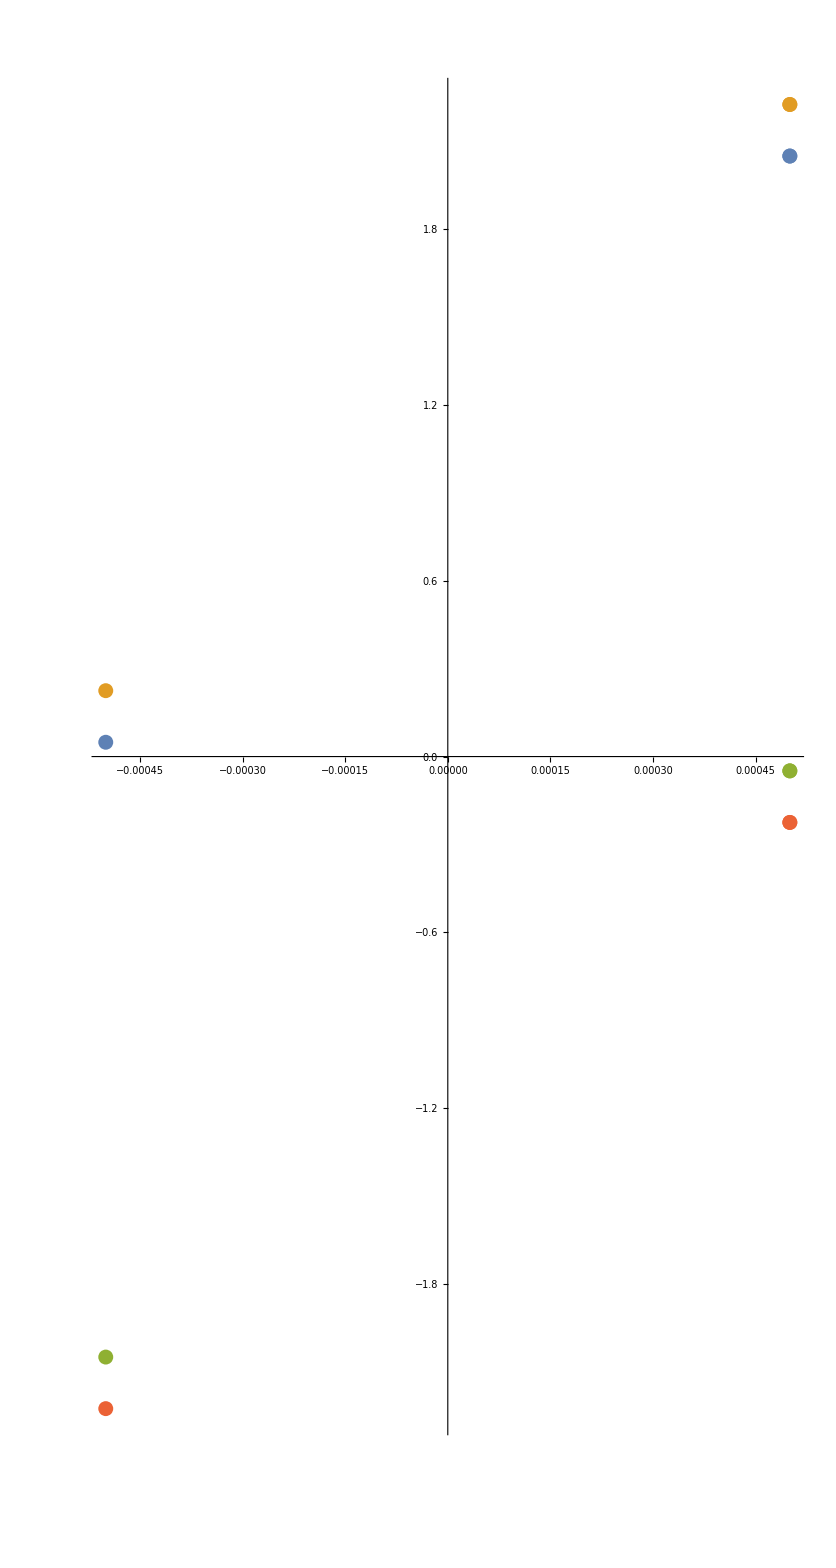

```mathematica
ComplexListPlot[{solution12,solution13,soll,soll1}]
```

```mathematica
p/.sol1[Sqrt[-1.1]]//N
```

{-0.0005+2.04881 ⅈ,0.0005+0.0488087 ⅈ}